```mathematica
data=Import["C:\\Users\\Nora\\Documents\\G1\\Lattice sum\\plot.csv","CSV"]
```

{{-3.,0.05,-1.,-4.53164×10^-15},{-3.,0.06,-0.999998,-5.91788×10^-15},{-3.,0.07,-1.,-6.21757×10^-15},57090,{3.,0.98,-0.175579,2.07937×10^-14},{3.,0.99,-0.170404,2.02145×10^-14}}
 |  |  |  |

```mathematica
Dimensions[data]
```

{57095,4}

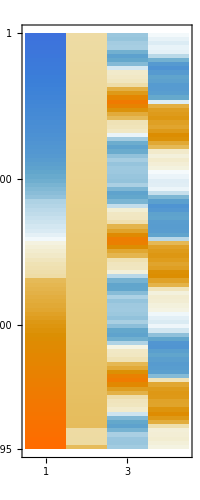

```mathematica
MatrixPlot[data]
```

```mathematica
realPart = data[[All,1;;3]]
```

{{-3.,0.05,-1.},{-3.,0.06,-0.999998},{-3.,0.07,-1.},{-3.,0.08,-0.999999},57088,{3.,0.97,-0.180902},{3.,0.98,-0.175579},{3.,0.99,-0.170404}}
 |  |  |  |

```mathematica
ListPlot3D[realPart,PlotRange->{All,{0.05,0.7},All},Mesh->None,ColorFunction->"Rainbow",AxesLabel->{x,y,"Re(theta(z))"}]
```

-Graphics3D-

```mathematica
imaPart = data[[All,{1,2,4}]]
```

{{-3.,0.05,-4.53164×10^-15},{-3.,0.06,-5.91788×10^-15},{-3.,0.07,-6.21757×10^-15},{-3.,0.08,-6.03002×10^-15},57088,{3.,0.97,2.13871×10^-14},{3.,0.98,2.07937×10^-14},{3.,0.99,2.02145×10^-14}}
 |  |  |  |

```mathematica
ListPlot3D[imaPart,PlotRange->{All,{0.05,0.7},All},Mesh->None,ColorFunction->"Rainbow",AxesLabel->{x,y,"Im(theta(z))"}]
```

-Graphics3D-